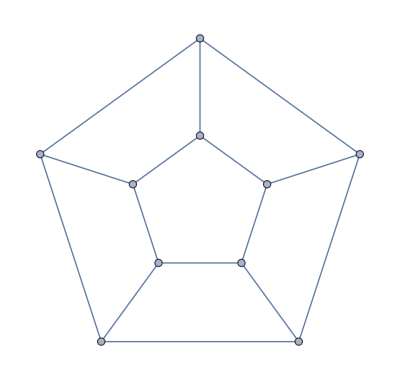

```mathematica
g=Graph[{1<-> 2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->7,3<->8,4<->9,5<->10,6<->7,7<->8,8<->9,9<->10,10<->6}, GraphLayout->"TutteEmbedding"]
```

```mathematica
emb=GraphEmbedding[g]
```

{{-1.83697×10^-16,1.},{-0.951057,0.309017},{-0.587785,-0.809017},{0.587785,-0.809017},{0.951057,0.309017},{-8.76402×10^-6,0.419826},{-0.399281,0.129736},{-0.246771,-0.339639},{0.246759,-0.339639},{0.399269,0.129735}}

```mathematica
emb2=Table[VertexList[g][[k]]->emb[[k]],{k,VertexCount[g]}]
```

{1→{-1.83697×10^-16,1.},2→{-0.951057,0.309017},3→{-0.587785,-0.809017},4→{0.587785,-0.809017},5→{0.951057,0.309017},6→{-8.76402×10^-6,0.419826},7→{-0.399281,0.129736},8→{-0.246771,-0.339639},9→{0.246759,-0.339639},10→{0.399269,0.129735}}

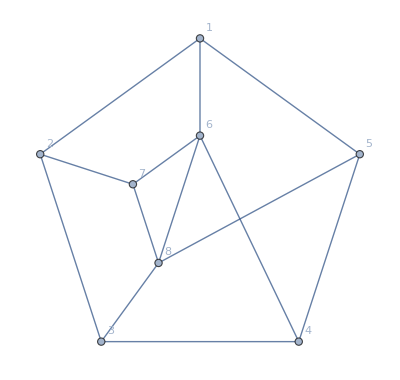

```mathematica
Graph[VertexContract[VertexContract[g,{6,9}],{8,10}], VertexCoordinates->Select[emb2,!MemberQ[{9,10},#[[1]]]&],VertexLabels->"Name"]
```

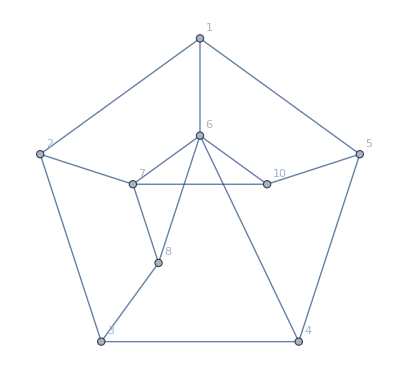

```mathematica
Graph[EdgeAdd[VertexContract[Graph[{6<->7,7<->8,8<->9,9<->10,10<->6,1<-> 2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->7,3<->8,4<->9,5<->10}],{6,9}],7<->10], VertexCoordinates->Select[emb2,!MemberQ[{9},#[[1]]]&],VertexLabels->"Name"]
```

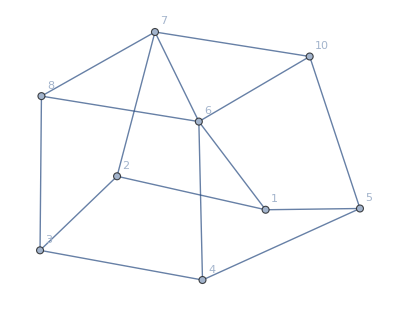

```mathematica
Graph[EdgeAdd[VertexContract[Graph[{6<->7,7<->8,8<->9,9<->10,10<->6,1<-> 2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->7,3<->8,4<->9,5<->10}],{6,9}],7<->10],VertexLabels->"Name"]
```

## second attempt

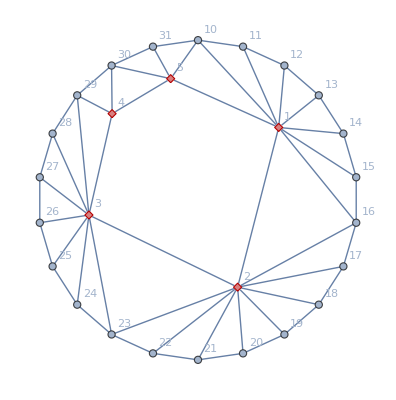

```mathematica
h=Graph[Join[{1<-> 2,2<->3,3<->4,4<->5,5<->1},Table[k<->k+1,{k,10,30}],{31<->10,5<->10},Table[1<->k,{k,10,16}],Table[2<->k,{k,16,23}],Table[3<->k,{k,23,29}],Table[4<->k,{k,29,30}],Table[5<->k,{k,30,31}]], GraphLayout->"TutteEmbedding"];Graph[h,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

```mathematica
emb=GraphEmbedding[h]
```

{{0.504912,0.45384},{0.247782,-0.545429},{-0.682298,-0.0940476},{-0.537416,0.540259},{-0.170975,0.758969},{-1.83697×10^-16,1.},{0.281733,0.959493},{0.540641,0.841254},{0.75575,0.654861},{0.909632,0.415415},{0.989821,0.142315},{0.989821,-0.142315},{0.909632,-0.415415},{0.75575,-0.654861},{0.540641,-0.841254},{0.281733,-0.959493},{6.12323×10^-17,-1.},{-0.281733,-0.959493},{-0.540641,-0.841254},{-0.75575,-0.654861},{-0.909632,-0.415415},{-0.989821,-0.142315},{-0.989821,0.142315},{-0.909632,0.415415},{-0.75575,0.654861},{-0.540641,0.841254},{-0.281733,0.959493}}

```mathematica
emb2=Table[VertexList[h][[k]]->emb[[k]],{k,VertexCount[h]}]
```

{1→{0.504912,0.45384},2→{0.247782,-0.545429},3→{-0.682298,-0.0940476},4→{-0.537416,0.540259},5→{-0.170975,0.758969},10→{-1.83697×10^-16,1.},11→{0.281733,0.959493},12→{0.540641,0.841254},13→{0.75575,0.654861},14→{0.909632,0.415415},15→{0.989821,0.142315},16→{0.989821,-0.142315},17→{0.909632,-0.415415},18→{0.75575,-0.654861},19→{0.540641,-0.841254},20→{0.281733,-0.959493},21→{6.12323×10^-17,-1.},22→{-0.281733,-0.959493},23→{-0.540641,-0.841254},24→{-0.75575,-0.654861},25→{-0.909632,-0.415415},26→{-0.989821,-0.142315},27→{-0.989821,0.142315},28→{-0.909632,0.415415},29→{-0.75575,0.654861},30→{-0.540641,0.841254},31→{-0.281733,0.959493}}

```mathematica
Graph[h,VertexCoordinates->emb2,VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

-Graphics-

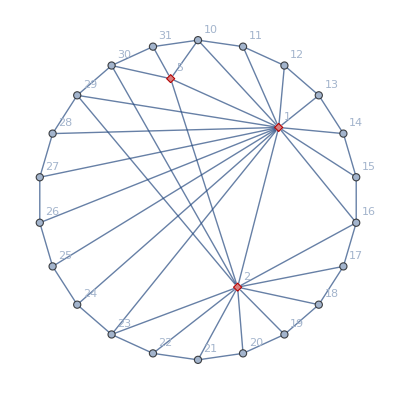

```mathematica
Graph[VertexContract[VertexContract[h,{1,3}],{2,4}],VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

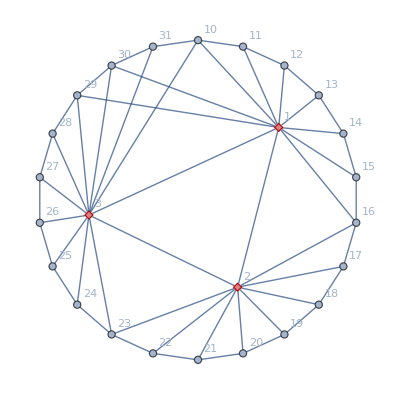

```mathematica
Graph[VertexContract[VertexContract[h,{1,4}],{3,5}],VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

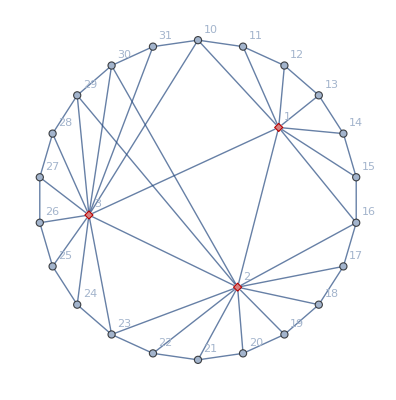

```mathematica
Graph[VertexContract[VertexContract[h,{2,4}],{3,5}],VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

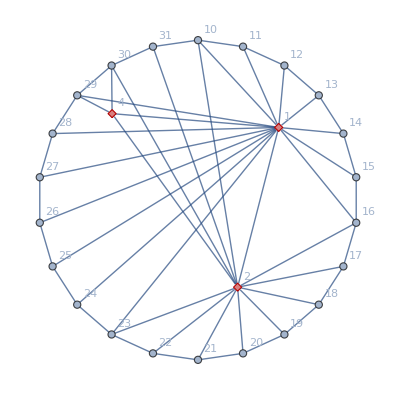

```mathematica
Graph[VertexContract[VertexContract[h,{1,3}],{2,5}],VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

```mathematica
Graph[VertexContract[VertexContract[h,{1,4}],{3,5}],VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

-Graphics-

```mathematica
Table[allGraphs[k,"graph"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[allGraphs[k,"graph"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

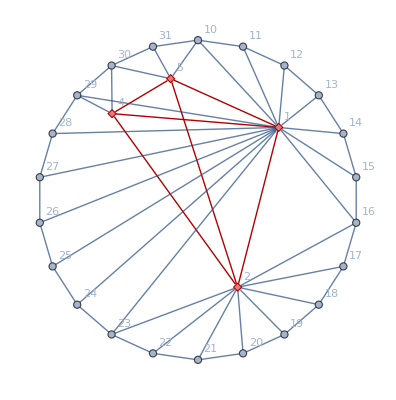

```mathematica
Graph[EdgeAdd[VertexContract[h,{1,3}],{2<->5,4<->2}],VertexCoordinates->emb2,VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5,1<->5,4<->5,1<->4,4<->2,1<->2,2<->5},GraphHighlightStyle->"VertexDiamond"]
```

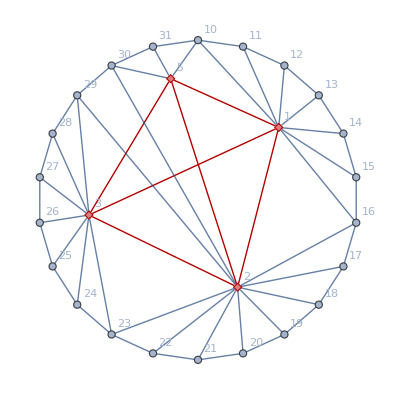

```mathematica
Graph[EdgeAdd[VertexContract[h,{2,4}],{3<->5,1<->3}],VertexCoordinates->emb2,VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5,1<->5,4<->5,1<->4,4<->2,1<->2,2<->5,3<->5,2<->3,1<->3},GraphHighlightStyle->"VertexDiamond"]
```

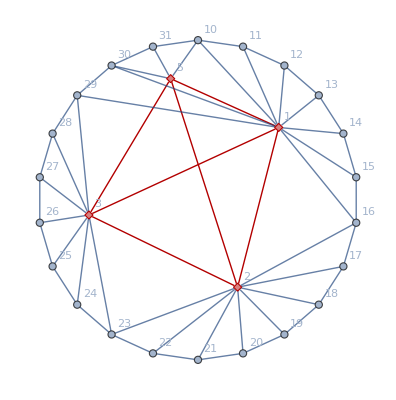

```mathematica
Graph[EdgeAdd[VertexContract[h,{1,4}],{2<->5,3<->5}],VertexCoordinates->emb2,VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5,1<->5,4<->5,1<->4,4<->2,1<->2,2<->5,3<->5,2<->3,1<->3,3<->4},GraphHighlightStyle->"VertexDiamond"]
```

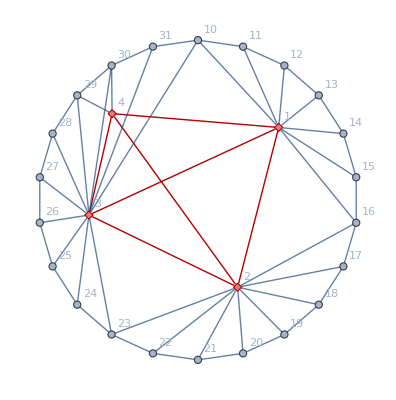

```mathematica
Graph[EdgeAdd[VertexContract[h,{3,5}],{4<->2,4<->1}],VertexCoordinates->emb2,VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5,1<->5,4<->5,1<->4,4<->2,1<->2,2<->5,3<->5,2<->3,1<->3,3<->4},GraphHighlightStyle->"VertexDiamond"]
```

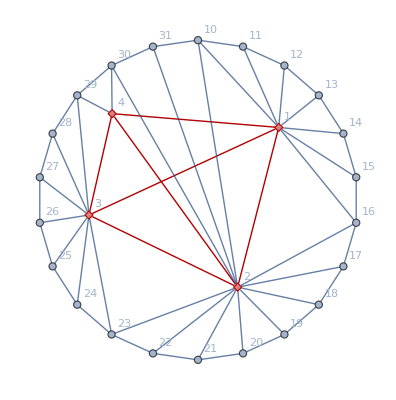

```mathematica
Graph[EdgeAdd[VertexContract[h,{2,5}],{3<->1,1<->4}],VertexCoordinates->emb2,VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5,1<->5,4<->5,1<->4,4<->2,1<->2,2<->5,3<->5,2<->3,1<->3,3<->4},GraphHighlightStyle->"VertexDiamond"]
```

```mathematica
g=Graph[EdgeAdd[VertexContract[h,{2,5}],{3<->1,1<->4}],VertexLabels->"Name",GraphHighlight->{1,2,3,4,5,1<->5,4<->5,1<->4,4<->2,1<->2,2<->5,3<->5,2<->3,1<->3,3<->4},GraphHighlightStyle->"VertexDiamond"];
```

```mathematica
CompleteBaseCoeff[ ChromaticPolynomial[g,x]]
```

{0,0,0,0,623220,7682635295,2912713753956,157870073451058,2388264034088788,14286887507196900,41462107789667875,66509353052533970,64416417354827426,40092223501648774,16775496893837401,4877564496688500,1009481971127717,151256918520951,16586363779145,1337888714633,79314465009,3428918982,106274987,2289161,32404,270,1}

```mathematica
CompleteBaseCoeff[ ChromaticPolynomial[VertexContract[g,14<->15],x]]
```

{0,0,0,0,304332,2556099457,727320127836,31426257845182,392797662853596,1984854966638274,4934642657637471,6841626899035285,5757476475570093,3121340075463287,1137846319707109,287670621037425,51557953060695,6646597675367,621235380903,42156078446,2064354809,71819167,1722791,26970,247,1}

```mathematica
CompleteBaseCoeff[ ChromaticPolynomial[VertexContract[g,{14,15,16}],x]]
```

{0,0,0,0,159444,856657535,181835153364,6251177357826,64433047436300,274360999582480,582549152498103,695460672235124,506204150342618,237740192827563,75008925730696,16358599907815,2514240028103,275490531801,21609053652,1208648526,47539238,1277891,22245,225,1}

```mathematica
gr[n_]:=If[
n==10,Graph[EdgeAdd[VertexContract[g,{1,3}],{2<->5,4<->2}],GraphLayout->"SpringElectricalEmbedding"],
Graph[DeleteDuplicates[EdgeList[Graph[EdgeAdd[
EdgeDelete[
VertexAdd[gr[n-1],n],{(n-2)<->(n-1)}],
{(n-2)<->n,(n-1)<->n,n<->5,11<->4}],VertexLabels->"Name"]
]]]]
```

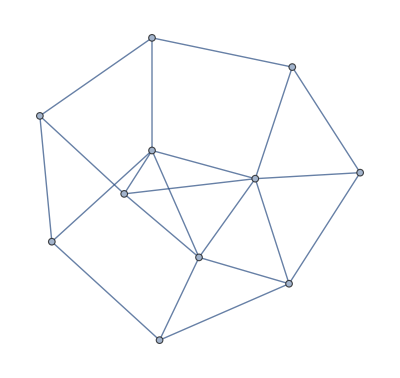

```mathematica
gr[12]
```

```mathematica
MatrixForm[Table[PadRight[CompleteBaseCoeff[ChromaticPolynomial[gr[n],x]],20],{n,11,18}]]
```

(0 | 0 | 0 | 0 | 77 | 674 | 1281 | 847 | 230 | 26 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 155 | 2106 | 5803 | 5517 | 2227 | 412 | 34 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 309 | 6466 | 25313 | 33387 | 18879 | 5111 | 684 | 43 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 619 | 19714 | 107723 | 192249 | 146661 | 54656 | 10583 | 1071 | 53 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1237 | 59754 | 450601 | 1068967 | 1072215 | 529253 | 139320 | 20222 | 1601 | 64 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2475 | 180506 | 1862163 | 5795437 | 7502257 | 4776986 | 1643813 | 321318 | 36232 | 2305 | 76 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4949 | 543986 | 7629153 | 30839347 | 50808979 | 40941159 | 17927490 | 4535675 | 683638 | 61587 | 3217 | 89 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 9899 | 1636914 | 31060603 | 161825889 | 335693221 | 337397092 | 184361079 | 58748565 | 11372055 | 1361095 | 100191 | 4374 | 103 | 1 | 0 | 0)

```mathematica
MatrixForm[Table[PadRight[NullBaseCoeff[ChromaticPolynomial[gr[n],x]],20],{n,10,20}]]
```

(0 | 636 | -2144 | 3113 | -2608 | 1402 | -500 | 116 | -16 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1926 | 7065 | -11405 | 10843 | -6767 | 2891 | -847 | 164 | -19 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4134 | -16789 | 30613 | -33470 | 24484 | -12565 | 4586 | -1175 | 202 | -21 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -8550 | 38445 | -78753 | 97932 | -82545 | 49630 | -21738 | 6936 | -1579 | 244 | -23 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 17382 | -86173 | 196689 | -274996 | 263129 | -181821 | 93107 | -35610 | 10094 | -2067 | 290 | -25 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -35046 | 190461 | -480289 | 747060 | -801361 | 626787 | -368036 | 164327 | -55798 | 14228 | -2647 | 340 | -27 | 1 | 0 | 0 | 0 | 0 | 0
0 | 70374 | -416701 | 1151777 | -1974788 | 2349889 | -2054951 | 1362860 | -696690 | 275923 | -84254 | 19522 | -3327 | 394 | -29 | 1 | 0 | 0 | 0 | 0
0 | -141030 | 904509 | -2720993 | 5101732 | -6674673 | 6459807 | -4780672 | 2756240 | -1248536 | 444431 | -123298 | 26176 | -4115 | 452 | -31 | 1 | 0 | 0 | 0
0 | 282342 | -1950781 | 6347233 | -12924836 | 18451185 | -19594303 | 16021152 | -10293152 | 5253312 | -2137398 | 691027 | -175650 | 34406 | -5019 | 514 | -33 | 1 | 0 | 0
0 | -564966 | 4184637 | -14645985 | 32197284 | -49827313 | 57639807 | -51636608 | 36607456 | -20799776 | 9528108 | -3519452 | 1042327 | -244462 | 44444 | -6047 | 580 | -35 | 1 | 0
0 | 1130214 | -8934973 | 33477345 | -79040932 | 131852017 | -165106943 | 160913024 | -124851520 | 78207008 | -39855992 | 16567012 | -5604106 | 1531251 | -333350 | 56538 | -7207 | 650 | -37 | 1)

```mathematica
gr2[n_]:=If[
n==10,Graph[VertexContract[VertexContract[g,{1,4}],{3,5}],GraphLayout->"SpectralEmbedding",VertexLabels->"Name"],
Graph[DeleteDuplicates[EdgeList[Graph[EdgeAdd[
EdgeDelete[
VertexAdd[gr[n-1],n],{(n-2)<->(n-1)}],
{(n-2)<->n,(n-1)<->n,n<->3,11<->1}]]
]],VertexLabels->"Name"]]
```

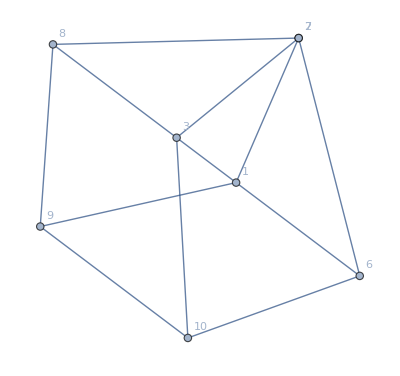

```mathematica
gr2[10]
```

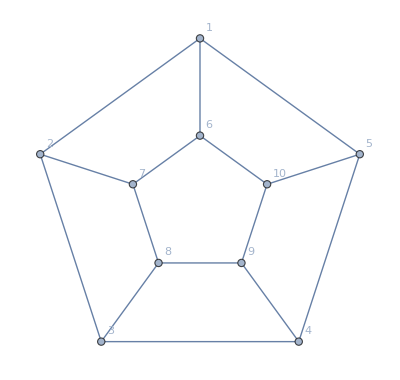

```mathematica
Graph[{1<-> 2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->7,3<->8,4<->9,5<->10,6<->7,7<->8,8<->9,9<->10,10<->6}, GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

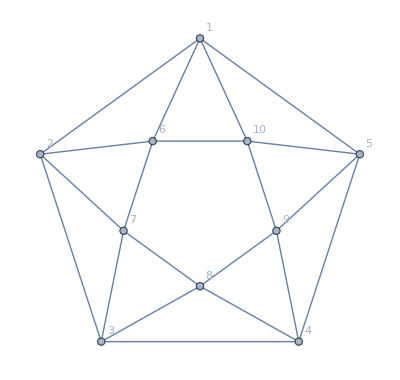

```mathematica
Graph[{1<-> 2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->7,3<->8,4<->9,5<->10,6<->7,7<->8,8<->9,9<->5,9<->10,2<->6,1<->10,3<->7,8<->4,6<->10}, GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
gr7[n_]:=Block[
{edges={1<-> 2,2<->3,3<->4,5<->1,1<->6,2<->7,3<->8,4<->9,5<->10,6<->7,7<->8,8<->9,9<->5,9<->10,2<->6,1<->10,3<->7,8<->4,6<->10},i,previous=4},
For[i=11,i≤n,i++,
AppendTo[edges,previous<->i];
AppendTo[edges,i<->9];
previous=i
];
AppendTo[edges,previous<->5];
Graph[edges, GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
]
```

```mathematica
gr7[10]
```

-Graphics-

## First the alpha graphs

```mathematica
MatrixForm[Table[PadRight[CompleteBaseCoeff[ChromaticPolynomial[VertexContract[VertexContract[gr7[n],{1,3}],{2,4}],x]],20],{n,10,18}]]
```

(0 | 0 | 0 | 0 | 4 | 23 | 28 | 10 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 6 | 75 | 139 | 79 | 16 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 14 | 229 | 627 | 533 | 175 | 23 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 26 | 703 | 2741 | 3293 | 1583 | 336 | 31 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 54 | 2133 | 11663 | 19205 | 12791 | 3935 | 584 | 40 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 106 | 6455 | 48789 | 107689 | 95951 | 40336 | 8607 | 944 | 50 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 214 | 19469 | 201607 | 587233 | 683395 | 378303 | 109192 | 17103 | 1444 | 61 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 426 | 58623 | 825901 | 3137773 | 4687603 | 3331516 | 1251839 | 263119 | 31543 | 2115 | 73 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 854 | 176293 | 3362223 | 16514765 | 31263391 | 28008215 | 13346228 | 3619910 | 578549 | 54808 | 2991 | 86 | 1 | 0 | 0 | 0)

```mathematica
MatrixForm[Table[PadRight[CompleteBaseCoeff[ChromaticPolynomial[VertexContract[VertexContract[gr7[n],{1,4}],{2,5}],x]],20],{n,10,18}]]
```

(0 | 0 | 0 | 0 | 4 | 23 | 28 | 10 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 50 | 107 | 68 | 15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12 | 177 | 506 | 457 | 159 | 22 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 20 | 520 | 2173 | 2781 | 1410 | 313 | 30 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 44 | 1603 | 9240 | 16088 | 11242 | 3601 | 553 | 39 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 84 | 4830 | 38535 | 89670 | 83539 | 36449 | 8025 | 904 | 49 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 172 | 14597 | 158998 | 486895 | 590905 | 338682 | 100649 | 16161 | 1394 | 60 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 340 | 43940 | 650561 | 2593463 | 4032324 | 2961679 | 1143874 | 246098 | 30101 | 2054 | 72 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 684 | 132183 | 2646212 | 13617886 | 26787408 | 24764077 | 12112671 | 3358756 | 547108 | 52695 | 2918 | 85 | 1 | 0 | 0 | 0)

```mathematica
MatrixForm[Table[PadRight[CompleteBaseCoeff[ChromaticPolynomial[VertexContract[VertexContract[gr7[n],{2,4}],{3,5}],x]],20],{n,10,18}]]
```

(0 | 0 | 0 | 0 | 4 | 23 | 28 | 10 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 50 | 107 | 68 | 15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12 | 177 | 506 | 457 | 159 | 22 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 20 | 520 | 2173 | 2781 | 1410 | 313 | 30 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 44 | 1603 | 9240 | 16088 | 11242 | 3601 | 553 | 39 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 84 | 4830 | 38535 | 89670 | 83539 | 36449 | 8025 | 904 | 49 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 172 | 14597 | 158998 | 486895 | 590905 | 338682 | 100649 | 16161 | 1394 | 60 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 340 | 43940 | 650561 | 2593463 | 4032324 | 2961679 | 1143874 | 246098 | 30101 | 2054 | 72 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 684 | 132183 | 2646212 | 13617886 | 26787408 | 24764077 | 12112671 | 3358756 | 547108 | 52695 | 2918 | 85 | 1 | 0 | 0 | 0)

```mathematica
MatrixForm[Table[PadRight[CompleteBaseCoeff[ChromaticPolynomial[VertexContract[VertexContract[gr7[n],{2,4}],{1,3}],x]],20],{n,10,18}]]
```

(0 | 0 | 0 | 0 | 4 | 23 | 28 | 10 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 6 | 75 | 139 | 79 | 16 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 14 | 229 | 627 | 533 | 175 | 23 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 26 | 703 | 2741 | 3293 | 1583 | 336 | 31 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 54 | 2133 | 11663 | 19205 | 12791 | 3935 | 584 | 40 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 106 | 6455 | 48789 | 107689 | 95951 | 40336 | 8607 | 944 | 50 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 214 | 19469 | 201607 | 587233 | 683395 | 378303 | 109192 | 17103 | 1444 | 61 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 426 | 58623 | 825901 | 3137773 | 4687603 | 3331516 | 1251839 | 263119 | 31543 | 2115 | 73 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 854 | 176293 | 3362223 | 16514765 | 31263391 | 28008215 | 13346228 | 3619910 | 578549 | 54808 | 2991 | 86 | 1 | 0 | 0 | 0)

```mathematica
MatrixForm[Table[PadRight[CompleteBaseCoeff[ChromaticPolynomial[VertexContract[VertexContract[gr7[n],{2,5}],{1,3}],x]],20],{n,10,18}]]
```

(0 | 0 | 0 | 0 | 4 | 23 | 28 | 10 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 6 | 75 | 139 | 79 | 16 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 14 | 229 | 627 | 533 | 175 | 23 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 26 | 703 | 2741 | 3293 | 1583 | 336 | 31 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 54 | 2133 | 11663 | 19205 | 12791 | 3935 | 584 | 40 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 106 | 6455 | 48789 | 107689 | 95951 | 40336 | 8607 | 944 | 50 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 214 | 19469 | 201607 | 587233 | 683395 | 378303 | 109192 | 17103 | 1444 | 61 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 426 | 58623 | 825901 | 3137773 | 4687603 | 3331516 | 1251839 | 263119 | 31543 | 2115 | 73 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 854 | 176293 | 3362223 | 16514765 | 31263391 | 28008215 | 13346228 | 3619910 | 578549 | 54808 | 2991 | 86 | 1 | 0 | 0 | 0)

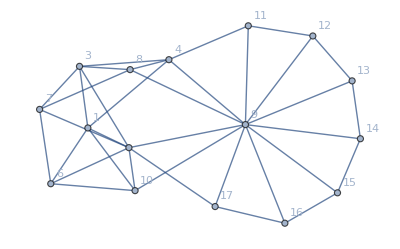

```mathematica
With[{h=gr7[17]},Graph[EdgeAdd[VertexContract[h,{2,5}],{3<->1,1<->4}],GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]]
```

## Quadrialterals

```mathematica
MatrixForm[Table[PadRight[CompleteBaseCoeff[ChromaticPolynomial[With[{h=gr7[n]},EdgeAdd[VertexContract[h,{2,5}],{3<->1,1<->4}]],x]],20],{n,10,18}]]
```

(0 | 0 | 0 | 0 | 6 | 55 | 111 | 69 | 15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 14 | 201 | 547 | 475 | 161 | 22 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 26 | 587 | 2341 | 2903 | 1439 | 315 | 30 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 54 | 1817 | 9999 | 16875 | 11539 | 3644 | 555 | 39 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 106 | 5475 | 41765 | 94355 | 86107 | 37047 | 8084 | 906 | 49 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 214 | 16561 | 172583 | 513559 | 610999 | 345436 | 101719 | 16238 | 1396 | 60 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 426 | 49867 | 706845 | 2740359 | 4179551 | 3029051 | 1159188 | 247861 | 30198 | 2056 | 72 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 854 | 150057 | 2877295 | 14408659 | 27817667 | 25382908 | 12302555 | 3389937 | 549841 | 52814 | 2920 | 85 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1706 | 450995 | 11659189 | 74920571 | 181314659 | 205498023 | 123803348 | 42811988 | 8888347 | 1130795 | 87854 | 4025 | 99 | 1 | 0 | 0)

```mathematica
MatrixForm[Table[PadRight[CompleteBaseCoeff[ChromaticPolynomial[With[{h=gr7[n]},EdgeAdd[VertexContract[h,{1,3}],{2<->5,4<->2}]],x]],20],{n,10,18}]]
```

(0 | 0 | 0 | 0 | 6 | 55 | 111 | 69 | 15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 18 | 215 | 555 | 476 | 161 | 22 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 30 | 619 | 2379 | 2915 | 1440 | 315 | 30 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 66 | 1931 | 10191 | 16974 | 11557 | 3645 | 555 | 39 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 126 | 5815 | 42639 | 95041 | 86314 | 37072 | 8085 | 906 | 49 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 258 | 17615 | 176427 | 517864 | 612927 | 345818 | 101752 | 16239 | 1396 | 60 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 510 | 53059 | 723267 | 2765727 | 4195424 | 3033653 | 1159834 | 247903 | 30199 | 2056 | 72 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1026 | 159731 | 2946183 | 14551922 | 27938273 | 25430995 | 12312325 | 3390961 | 549893 | 52815 | 2920 | 85 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2046 | 480175 | 11944407 | 75705773 | 182181558 | 205955238 | 123929595 | 42830974 | 8889891 | 1130858 | 87855 | 4025 | 99 | 1 | 0 | 0)

```mathematica
MatrixForm[Table[PadRight[CompleteBaseCoeff[ChromaticPolynomial[With[{h=gr7[n]},EdgeAdd[VertexContract[h,{2,4}],{3<->5,1<->3}]],x]],20],{n,10,18}]]
```

(0 | 0 | 0 | 0 | 6 | 55 | 111 | 69 | 15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 14 | 201 | 547 | 475 | 161 | 22 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 26 | 587 | 2341 | 2903 | 1439 | 315 | 30 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 54 | 1817 | 9999 | 16875 | 11539 | 3644 | 555 | 39 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 106 | 5475 | 41765 | 94355 | 86107 | 37047 | 8084 | 906 | 49 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 214 | 16561 | 172583 | 513559 | 610999 | 345436 | 101719 | 16238 | 1396 | 60 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 426 | 49867 | 706845 | 2740359 | 4179551 | 3029051 | 1159188 | 247861 | 30198 | 2056 | 72 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 854 | 150057 | 2877295 | 14408659 | 27817667 | 25382908 | 12302555 | 3389937 | 549841 | 52814 | 2920 | 85 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1706 | 450995 | 11659189 | 74920571 | 181314659 | 205498023 | 123803348 | 42811988 | 8888347 | 1130795 | 87854 | 4025 | 99 | 1 | 0 | 0)

```mathematica
MatrixForm[Table[PadRight[CompleteBaseCoeff[ChromaticPolynomial[With[{h=gr7[n]},EdgeAdd[VertexContract[h,{1,4}],{2<->5,3<->5}]],x]],20],{n,10,18}]]
```

(0 | 0 | 0 | 0 | 6 | 55 | 111 | 69 | 15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 6 | 116 | 388 | 387 | 144 | 21 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 18 | 409 | 1779 | 2392 | 1266 | 292 | 29 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 30 | 1190 | 7414 | 13670 | 9973 | 3309 | 524 | 38 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 66 | 3655 | 30957 | 75833 | 73523 | 33137 | 7501 | 866 | 48 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 126 | 10976 | 127372 | 410053 | 516956 | 305481 | 93145 | 15295 | 1346 | 59 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 258 | 33109 | 520575 | 2177706 | 3511804 | 2655324 | 1050641 | 230800 | 28755 | 1995 | 71 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 510 | 99530 | 2115298 | 11409036 | 23248515 | 22099071 | 11060452 | 3127841 | 518350 | 50700 | 2847 | 84 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1026 | 299155 | 8560833 | 59160547 | 150900141 | 177942013 | 110582687 | 39211021 | 8311341 | 1076050 | 84864 | 3939 | 98 | 1 | 0 | 0)

```mathematica
MatrixForm[Table[PadRight[CompleteBaseCoeff[ChromaticPolynomial[With[{h=gr7[n]},EdgeAdd[VertexContract[h,{3,5}],{4<->2,4<->1}]],x]],20],{n,10,18}]]
```

(0 | 0 | 0 | 0 | 6 | 55 | 111 | 69 | 15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 6 | 116 | 388 | 387 | 144 | 21 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 18 | 409 | 1779 | 2392 | 1266 | 292 | 29 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 30 | 1190 | 7414 | 13670 | 9973 | 3309 | 524 | 38 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 66 | 3655 | 30957 | 75833 | 73523 | 33137 | 7501 | 866 | 48 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 126 | 10976 | 127372 | 410053 | 516956 | 305481 | 93145 | 15295 | 1346 | 59 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 258 | 33109 | 520575 | 2177706 | 3511804 | 2655324 | 1050641 | 230800 | 28755 | 1995 | 71 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 510 | 99530 | 2115298 | 11409036 | 23248515 | 22099071 | 11060452 | 3127841 | 518350 | 50700 | 2847 | 84 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1026 | 299155 | 8560833 | 59160547 | 150900141 | 177942013 | 110582687 | 39211021 | 8311341 | 1076050 | 84864 | 3939 | 98 | 1 | 0 | 0)